# Parameter scan for local clustering model

## Supplementary material for Fischer et al "The salt-and-pepper pattern in mouse blastocysts is compatible with signalling beyond the nearest neighbours."

## Initialisation

```mathematica
baseDirectory=StringReplace[ParentDirectory[NotebookDirectory[]],"dataPreprocessing"->"analysisCode"];
```

```mathematica
<<(FileNameJoin[{baseDirectory,"CellNucleiSegmentation_v8.m"}]) (*code from Schmitz et al. Scientific Reports 2017*)
```

```mathematica
<<(FileNameJoin[{baseDirectory,"neighbourAnaFunctions_v2.m"}])(*code from Fischer et al. PLOS One 2020 and extensions*)
```

```mathematica
shiftValue[expName_,val_,threshold_,experiments_]:=Switch[expName,experiments[[1,1]],val+(threshold[[1]]-threshold[[1]]),experiments[[2,1]],val+(threshold[[1]]-threshold[[2]]),experiments[[3,1]],val+(threshold[[1]]-threshold[[3]]),experiments[[4,1]],val+(threshold[[1]]-threshold[[4]])]
```

```mathematica
zCorrection[fileName_,slope_,channels_:{"Dapi","Nanog","Gata6","Gata4"}]:=Block[{nucleiFeatures,nucleiFeaturesWithCorr,exportFName},
nucleiFeatures="NucleiFeatures"/.Import[fileName];
nucleiFeaturesWithCorr=Join[#,
Table[channels[[i]]<>"-AvgLnCorr"->Log[channels[[i]]<>"-Avg"/.#]-slope[[i]]*("Centroid"/.#)[[3]],{i,1,Length[channels]}]&@#]&/@nucleiFeatures;
exportFName=StringReplace[fileName,"Features.mx"->"Features_ZCorrected.mx"];
Export[exportFName,"NucleiFeatures"->nucleiFeaturesWithCorr]
]
```

```mathematica
fontOption="Arial";
```

```mathematica
<<ErrorBarPlots`
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
plotMeanStdLighter[xValues_,yValues_,smooth_,xLabel_,yLabel_,colour_]:=
Show[Table[ListLinePlot[{Transpose[{xValues[[i]],MeanFilter[#[[All,1]]+#[[All,2]],smooth]}],
Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]}&@yValues[[i]],PlotRange->{0,All},
PlotStyle->{Directive[Opacity[0.5],Lighter[colour[i],0.7]],Directive[Opacity[0.5],Lighter[colour[i],0.7]]},Filling->1->{2},FillingStyle->Directive[Opacity[0.5],Lighter[colour[i],0.5]],Frame->{True,True,None,None},FrameStyle->Directive[Black,(*Thick,*)FontFamily->fontOption,14],(*TicksStyle->Thick,*)FrameLabel->{xLabel,yLabel}],{i,1,Length[xValues]}],
ListLinePlot[Table[Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]],{i,1,Length[xValues]}],
PlotRange->{0,All},PlotStyle->Transpose[{ConstantArray[Thickness[0.007],Length[xValues]],Table[colour[i],{i,1,Length[xValues]}]}],Frame->{True,True,None,None},FrameStyle->Directive[Black,FontFamily->fontOption,14],FrameLabel->{xLabel,yLabel}]]
```

```mathematica
smoothedValues[unsmoothedData_,smooth_]:=Block[{xValues,yValues,lowerLimit,mean},
xValues=#[[All,1]]&/@unsmoothedData;
yValues=#[[All,2;;3]]&/@unsmoothedData;
Table[lowerLimit=Transpose[{xValues[[i]],MeanFilter[#[[All,1]]-#[[All,2]],smooth]}]&@yValues[[i]];mean=Transpose[{xValues[[i]],MeanFilter[#[[All,1]],smooth]}]&@yValues[[i]];Table[Join[mean[[i]],{(mean-lowerLimit)[[i,-1]]}],{i,1,Length[mean]}],{i,1,Length[xValues]}]
]
```

```mathematica
colourNegPos[i_]:={Lighter[Gray,0.3],Darker[Gray,0.7]}[[i]]
```

```mathematica
colour3[i_]:=Join[{Darker[Gray]},(ColorData[16]/@{3,6,4})][[i]]
```

```mathematica
colour2[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7]}[[i]]
```

```mathematica
colour1[i_]:={Darker[Gray],Darker[Purple],Darker[Green,0.7],Darker[Cyan,0.5]}[[i]]
```

```mathematica
populationsColours={Lighter[Orange,0.7],Gray,Darker[Purple],Darker[Green,0.7]};
```

```mathematica
calcPlotRatioSortedByCellNumber[exprCell_,exprNeigh_,comp_,stages_,cellNumberPerEmbryo_,fateExcluded_:"TE"]:=Block[{cellPosPosNeighPropAll,numNeigh,cellNumbers,numPosCells,numNegCells,cellNegNegNeighPropAll,plotRatios},
cellPosPosNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprCell<>"+"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
cellNumbers=Table[Length[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&]],{i,1,Length[comp]}];
numPosCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]],{i,1,Length[comp]}];
numNegCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]],{i,1,Length[comp]}];
cellNegNegNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprNeigh<>"-"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
plotRatios=MapThread[Rule,{{"Stage","CellNumberEmbryo","CellNumberICM","NumPosCellsICM","NumNegCellsICM","MeanRatioNegNeighbNegCell","SEMRatioNegNeighbNegCell","MeanRatioPosNeighbPosCell","SEMRatioPosNeighbPosCell"},#}]&/@Table[{stages[[i]],cellNumberPerEmbryo[[i]],cellNumbers[[i]],numPosCells[[i]],numNegCells[[i]],Mean[cellNegNegNeighPropAll[[i]]],If[Length[cellNegNegNeighPropAll[[i]]]>1,(StandardDeviation[cellNegNegNeighPropAll[[i]]]/Sqrt[Length[cellNegNegNeighPropAll[[i]]]]),0],
Mean[cellPosPosNeighPropAll[[i]]],If[Length[cellPosPosNeighPropAll[[i]]]>1,(StandardDeviation[cellPosPosNeighPropAll[[i]]]/Sqrt[Length[cellPosPosNeighPropAll[[i]]]]),0]},{i,1,Length[cellNumbers]}];
SortBy[plotRatios,"CellNumber"/.#&]
]
```

```mathematica
calcPlotRatioAllCells[exprCell_,exprNeigh_,comp_,stages_,cellNumberPerEmbryo_,fateExcluded_:"TE"]:=Block[{cellPosPosNeighPropAll,numNeigh,cells,cellNumbers,cellNegNegNeighPropAll,plotRatios,numPosCells,numNegCells,centroids,distancesToCentroids},
cellPosPosNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprCell<>"+"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
cellNumbers=Table[Length[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&]],{i,1,Length[comp]}];
numPosCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"+"]],{i,1,Length[comp]}];
numNegCells=Table[Count[Select[comp[[i,2]],#[[1,1]]≠fateExcluded&][[All,1,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]],{i,1,Length[comp]}];
cellNegNegNeighPropAll=Select[#,NumberQ]&/@Table[If[(numNeigh=Length[Select[#,#[[1]]≠fateExcluded&]])>0,Count[Select[#,#[[1]]≠fateExcluded&][[All,2]],z_/;StringContainsQ[z,exprNeigh<>"-"]]/numNeigh,"NA"]&/@(Select[comp[[i,2]],#[[1,1]]≠fateExcluded&&StringContainsQ[#[[1,2]],exprNeigh<>"-"]&][[All,2,All,2;;3]]),{i,1,Length[comp]}];
MapThread[Rule,{{"Stage","CellNumberEmbryo","CellNumberICM","NumPosCellsICM","NumNegCellsICM","RatiosNegNeighbNegCell","RatiosPosNeighbPosCell"},#}]&/@Table[{stages[[i]],cellNumberPerEmbryo[[i]],cellNumbers[[i]],numPosCells[[i]],numNegCells[[i]],cellNegNegNeighPropAll[[i]],cellPosPosNeighPropAll[[i]]},{i,1,Length[cellNumbers]}]
]
```

```mathematica
calcDistances[comp_,exprCell_]:=Block[{cells,centroids,maxDistanceToCentroid,distancesToCentroids,distancesPositive,distancesNegative},
cells=Table[Select[comp[[i,2,All,1]],#[[1]]≠"TE"&],{i,1,Length[comp]}];
centroids=Mean[#[[All,3]]]&/@cells;
distancesToCentroids=Table[EuclideanDistance[#,centroids[[i]]]&/@cells[[i,All,3]],{i,1,Length[cells]}];
maxDistanceToCentroid=Max/@distancesToCentroids;
distancesPositive=Table[Pick[distancesToCentroids[[i]],cells[[i,All,2]],z_/;StringContainsQ[z,exprCell<>"+"]],{i,1,Length[cells]}];
distancesNegative=Table[Pick[distancesToCentroids[[i]],cells[[i,All,2]],z_/;StringContainsQ[z,exprCell<>"-"]],{i,1,Length[cells]}];
Table[{"Stage"->comp[[i,1]],"maxDistanceToCentroid"->maxDistanceToCentroid[[i]],"distancesToCentroids"->distancesToCentroids[[i]],"distancesPositive"->distancesPositive[[i]],"distancesNegative"->distancesNegative[[i]]},{i,1,Length[comp]}]
]
```

## Pattern generation

```mathematica
finalFNames=Join[FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"simulations"->"JLG_2021_NG6"],"EmbryoFeatures"}]],
FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"simulations"->"SMD_2021_NG6G4"],"EmbryoFeatures"}]],
FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"simulations"->"SMD_2020_NG6"],"EmbryoFeatures"}]],
FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"simulations"->"NS_2020_NRatG6Rb"],"EmbryoFeatures"}]],
FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"simulations"->"NS_2020_NRatG6Gt"],"EmbryoFeatures"}]],
FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"simulations"->"NS_2016_NG6"],"EmbryoFeatures"}]],
FileNames["*FinalData.mx",FileNameJoin[{StringReplace[NotebookDirectory[],"simulations"->"NS_2020_NG6"],"EmbryoFeatures"}]]];
```

```mathematica
Length[finalFNames]
```

738

also includes stage 3.0 embryos that are discarded later

```mathematica
data=Import/@finalFNames;
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];
```

#### Functions for local clustering

```mathematica
fateCluster[centroids_,dcgGraph_,valPos_,valNeg_,propClust_]:=Block[{sortedCentroids,fateVal},
sortedCentroids=Nest[Join[#,Nearest[Complement[centroids,#],#[[-1]],DistanceFunction->(GraphDistance[dcgGraph,#1,#2]&)]]&,{centroids[[1]]},Length[centroids]-1];
fateVal=NestList[If [RandomReal[]<=propClust,#,Abs[1-#]]&,RandomInteger[],Length[sortedCentroids]];
Table[{If[fateVal[[i]]==1,valPos,valNeg],sortedCentroids[[i]]},{i,1,Length[sortedCentroids]}]
]
```

```mathematica
generateLocalCluster[nuclei_,dcgGraph_,propClust_,exprCell_]:=Block[{cluster,centroids,pattern,rules},
centroids="Centroid"/.nuclei;
pattern=fateCluster[centroids,dcgGraph,exprCell<>"+",exprCell<>"-",propClust];
rules=Rule[#[[2]],#[[1]]]&/@pattern;
Join[#,{("localClusterFate"<>ToString[propClust]<>exprCell)->(("Centroid"/.#)/.rules)}]&/@nuclei
]
```

#### TE cells

```mathematica
generateTE[nuclei_,exprCell_,propClust_]:=Table[Join[nuclei[[i]],{"randomFate"<>exprCell->"TE","nearestNeighFate"<>exprCell->"TE","periodTwoIFate"<>exprCell->"TE","periodTwoIIFate"<>exprCell->"TE","localClusterFate"<>ToString[propClust]<>exprCell->"TE"}],{i,1,Length[nuclei]}]
```

### Assignment

```mathematica
Table[Print[j];
simulationData=Table[If[Mod[i,100]==0,Print[i]];
(exprCell="";
nuclei=Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&];
nucleiTE=Complement[nucleiFeatures[[i]],nuclei];
dcgGraph=dcgGraphs[[i,2]];
nucleiTE=Fold[generateTE[#1,exprCell,#2]&,nucleiTE,Range[0,1,0.1]];
nuclei=Fold[generateLocalCluster[#1,dcgGraph,#2,exprCell]&,nuclei,Range[0,1,0.1]];
Join[nucleiTE,nuclei]),{i,1,Length[nucleiFeatures]}];
Print[Tally[Table[Sort[("Centroid"/.simulationData[[i]])]==Sort[("Centroid"/.nucleiFeatures[[i]])],{i,1,Length[nucleiFeatures]}]]];
globalFeatures="GlobalFeatures"/.data;
exportData=Table[{"NucleiFeatures"->simulationData[[i]],"GlobalFeatures"->globalFeatures[[i]],"Staging"->staging[[i]]},{i,1,Length[simulationData]}];
Export[FileNameJoin[{NotebookDirectory[],"Results\\Simulations_localClustAll"<>ToString[j]<>"_FinalData.mx"}],exportData],{j,1,5}]
```

```mathematica
Table[Print[j];
simulationData=Table[If[Mod[i,100]==0,Print[i]];
(exprCell="";
nuclei=Select[nucleiFeatures[[i]],("TE/ICM"/.#)≠"TE"&];
nucleiTE=Complement[nucleiFeatures[[i]],nuclei];
dcgGraph=dcgGraphs[[i,2]];
nucleiTE=generateTE[nucleiTE,exprCell,0.55];
nuclei=generateLocalCluster[nuclei,dcgGraph,0.55,exprCell];
Join[nucleiTE,nuclei]),{i,1,Length[nucleiFeatures]}];
Print[Tally[Table[Sort[("Centroid"/.simulationData[[i]])]==Sort[("Centroid"/.nucleiFeatures[[i]])],{i,1,Length[nucleiFeatures]}]]];
globalFeatures="GlobalFeatures"/.data;
exportData=Table[{"NucleiFeatures"->simulationData[[i]],"GlobalFeatures"->globalFeatures[[i]],"Staging"->staging[[i]]},{i,1,Length[simulationData]}];
Export[FileNameJoin[{NotebookDirectory[],"Results\\Simulations_localClust0.55"<>ToString[j]<>"_FinalData.mx"}],exportData],{j,1,5}]
```

## Calculate and export neighbour comparison files (random, multiple replicates)

```mathematica
finalFNames=Select[FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"Results"}]],StringContainsQ[#,"_localClustAll"]&];
```

these data sets differ for the random, the nearest neighbour and the local clustering model

```mathematica
data=Flatten[Import[#]&/@finalFNames,1];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];
```

```mathematica
nucleiFeatures[[1,1]]
```

{Inlier/Outlier→1,EmbryoId→1,CellID→2,Size→208.121,TE/ICM→TE,Centroid→{72.9094,62.8042,0.00637535},Dapi-Avg→101.94,Dapi-Sum→218000.,Nanog-Avg→4.1146,Nanog-Sum→8797,Gata6-Avg→26.051,Gata6-Sum→55696,Total-Avg→3.1852,Total-Sum→6810,Dapi-AvgLnCorr→4.66276,Nanog-AvgLnCorr→1.45542,Gata6-AvgLnCorr→3.31466,Total-AvgLnCorr→1.20368,SurfaceDistance→0.,SurfaceNearest→{72.9094,62.8042,0.00637535},PCGNeighborCount→10.,PCGClusteringCoefficient→0.822222,PCGMinNeighborDistance→10.7248,PCGMaxNeighborDistance→29.1671,PCGMeanNeighborDistance→20.5955,PCGStandardDeviationNeighborDistance→7.10729,DCGNeighborCount→7.,DCGClusteringCoefficient→0.714286,DCGMinNeighborDistance→10.7248,DCGMaxNeighborDistance→29.0926,DCGMeanNeighborDistance→17.8414,DCGStandardDeviationNeighborDistance→6.71144,Dapi-AvgNorm→0.402612,Nanog-AvgNorm→0.020916,Gata6-AvgNorm→0.145266,Total-AvgNorm→0.0182754,Dapi-AvgNorm→0.402612,Nanog-AvgNorm→0.020916,Gata6-AvgNorm→0.145266,Total-AvgNorm→0.0182754,Nanog-AvgShifted→22.4863,Gata6-AvgShifted→49.313,Quadrant→N-G6-,localClusterFate0.→TE,localClusterFate0.1→TE,localClusterFate0.2→TE,localClusterFate0.3→TE,localClusterFate0.4→TE,localClusterFate0.5→TE,localClusterFate0.6→TE,localClusterFate0.7→TE,localClusterFate0.8→TE,localClusterFate0.9→TE,localClusterFate1.→TE}

#### Local cluster

```mathematica
(*(compLocalClust=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Expr","Expr","localClusterFate"<>ToString[#]];
Export[FileNameJoin[{NotebookDirectory[],"Results\\quadrantsComp_LocalClust"<>ToString[#]<>".mx"}],compLocalClust])&/@Range[0,1,0.1]*)
```

```mathematica
(*(compLocalClust=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Expr","Expr","localClusterFate"<>ToString[#]];
Export[FileNameJoin[{NotebookDirectory[],"Results\\quadrantsComp_LocalClust"<>ToString[#]<>".mx"}],compLocalClust])&/@Range[0.8,1,0.1]*)
```

### 0.55

```mathematica
finalFNames=Select[FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"Results"}]],StringContainsQ[#,"_localClust0.55"]&];
```

```mathematica
data=Flatten[Import[#]&/@finalFNames,1];
```

```mathematica
nucleiFeatures=("NucleiFeatures"/.data);
```

```mathematica
staging=("Staging"/.data);
```

```mathematica
dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];
```

```mathematica
nucleiFeatures[[1,1]]
```

{Inlier/Outlier→1,EmbryoId→1,CellID→2,Size→208.121,TE/ICM→TE,Centroid→{72.9094,62.8042,0.00637535},Dapi-Avg→101.94,Dapi-Sum→218000.,Nanog-Avg→4.1146,Nanog-Sum→8797,Gata6-Avg→26.051,Gata6-Sum→55696,Total-Avg→3.1852,Total-Sum→6810,Dapi-AvgLnCorr→4.66276,Nanog-AvgLnCorr→1.45542,Gata6-AvgLnCorr→3.31466,Total-AvgLnCorr→1.20368,SurfaceDistance→0.,SurfaceNearest→{72.9094,62.8042,0.00637535},PCGNeighborCount→10.,PCGClusteringCoefficient→0.822222,PCGMinNeighborDistance→10.7248,PCGMaxNeighborDistance→29.1671,PCGMeanNeighborDistance→20.5955,PCGStandardDeviationNeighborDistance→7.10729,DCGNeighborCount→7.,DCGClusteringCoefficient→0.714286,DCGMinNeighborDistance→10.7248,DCGMaxNeighborDistance→29.0926,DCGMeanNeighborDistance→17.8414,DCGStandardDeviationNeighborDistance→6.71144,Dapi-AvgNorm→0.402612,Nanog-AvgNorm→0.020916,Gata6-AvgNorm→0.145266,Total-AvgNorm→0.0182754,Dapi-AvgNorm→0.402612,Nanog-AvgNorm→0.020916,Gata6-AvgNorm→0.145266,Total-AvgNorm→0.0182754,Nanog-AvgShifted→22.4863,Gata6-AvgShifted→49.313,Quadrant→N-G6-,randomFate→TE,nearestNeighFate→TE,periodTwoIFate→TE,periodTwoIIFate→TE,localClusterFate0.55→TE}

```mathematica
(*(compLocalClust=compareValPopNeighboursFun[nucleiFeatures,dcgGraphs,"Expr","Expr","localClusterFate"<>ToString[#]];
Export[FileNameJoin[{NotebookDirectory[],"Results\\quadrantsComp_LocalClust"<>ToString[#]<>".mx"}],compLocalClust])&@0.55*)
```

## ICM composition scatter plots

```mathematica
quadrantsCompAll=Import[FileNameJoin[{NotebookDirectory[],"Results\\quadrantsComp_LocalClust"<>ToString[#]<>".mx"}]]&/@Range[0,1,0.1];
```

### 0<p<1

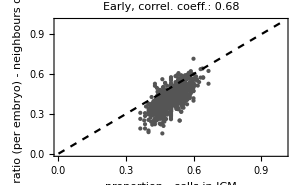
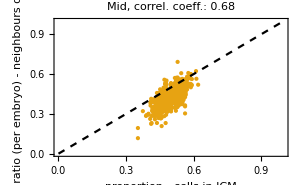
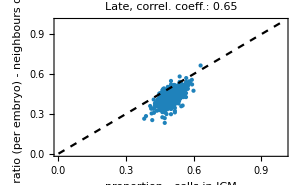
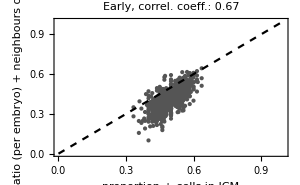
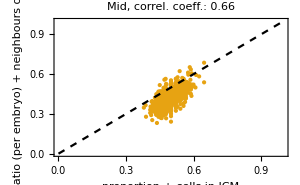
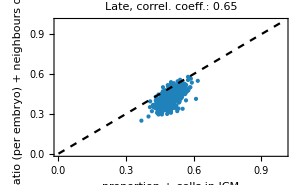
{            -Graphics--Graphics--Graphics-{negative, p=0.1},            -Graphics--Graphics--Graphics-{positive, p=0.1}}

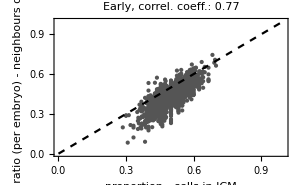
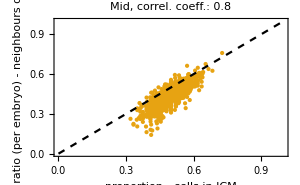
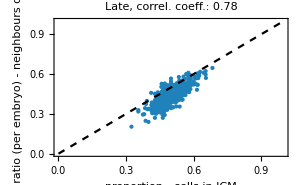
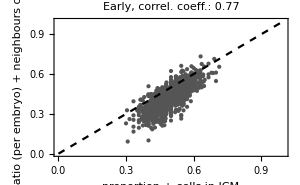
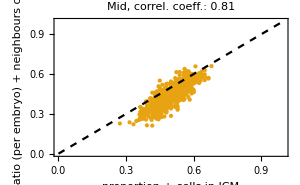
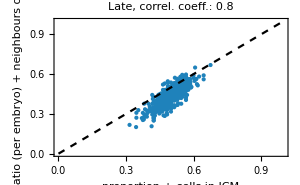
{            -Graphics--Graphics--Graphics-{negative, p=0.2},            -Graphics--Graphics--Graphics-{positive, p=0.2}}

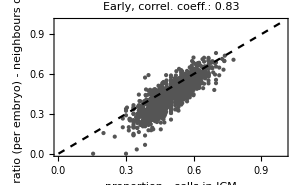
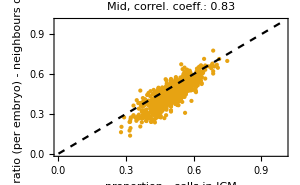
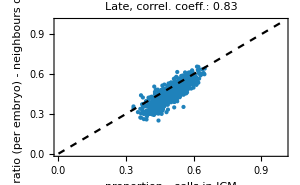
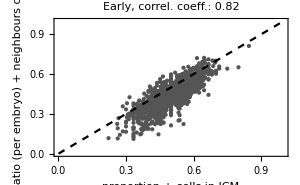
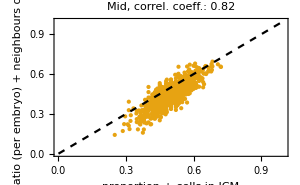
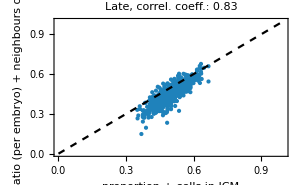
{            -Graphics--Graphics--Graphics-{negative, p=0.3},            -Graphics--Graphics--Graphics-{positive, p=0.3}}

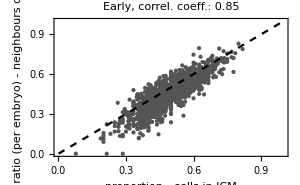
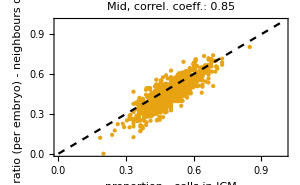
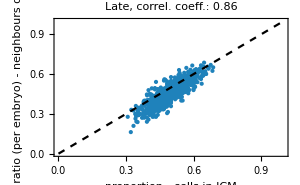
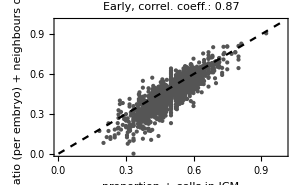
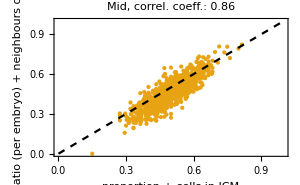
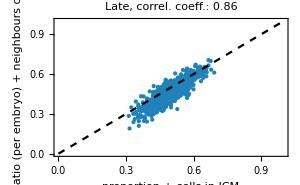
{            -Graphics--Graphics--Graphics-{negative, p=0.4},            -Graphics--Graphics--Graphics-{positive, p=0.4}}

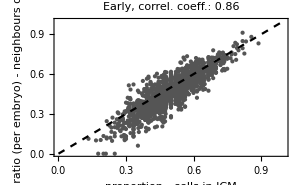
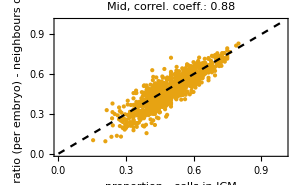
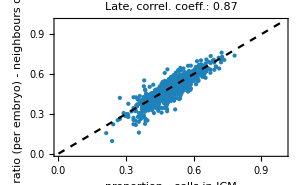
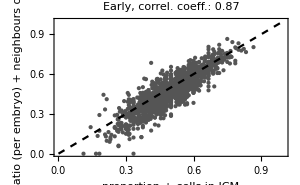
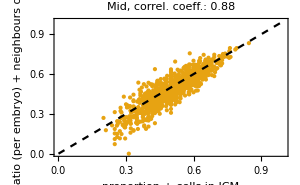
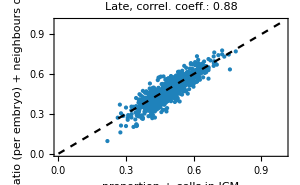
{            -Graphics--Graphics--Graphics-{negative, p=0.5},            -Graphics--Graphics--Graphics-{positive, p=0.5}}

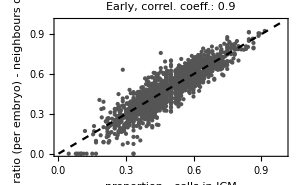
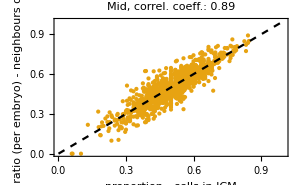
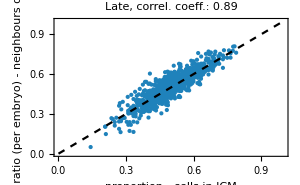
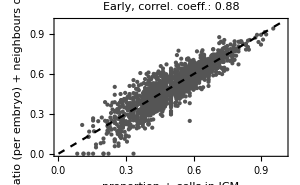
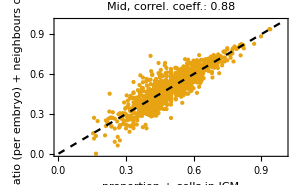
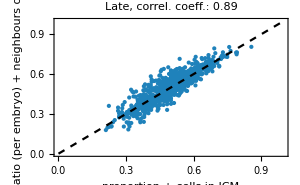
{            -Graphics--Graphics--Graphics-{negative, p=0.6},            -Graphics--Graphics--Graphics-{positive, p=0.6}}

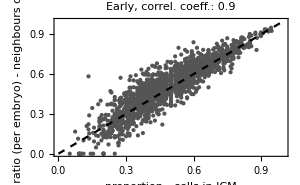
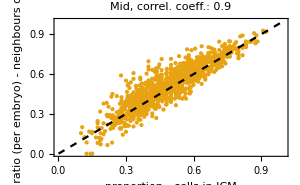
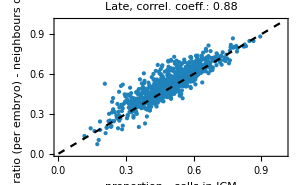
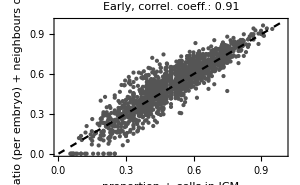
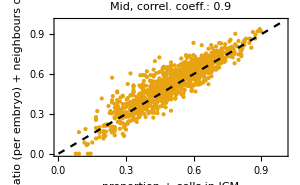
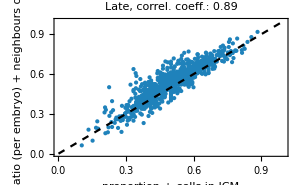
{            -Graphics--Graphics--Graphics-{negative, p=0.7},            -Graphics--Graphics--Graphics-{positive, p=0.7}}

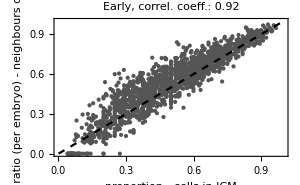
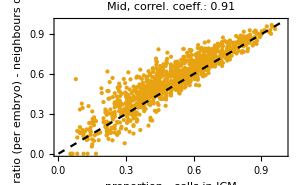
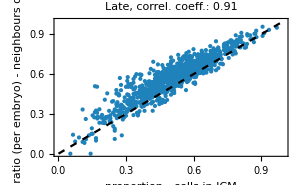
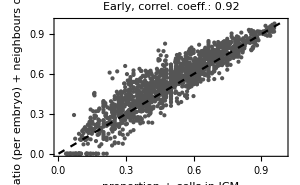
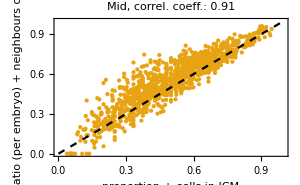
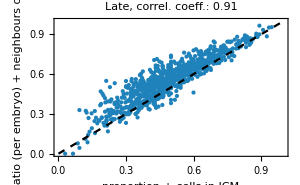
{            -Graphics--Graphics--Graphics-{negative, p=0.8},            -Graphics--Graphics--Graphics-{positive, p=0.8}}

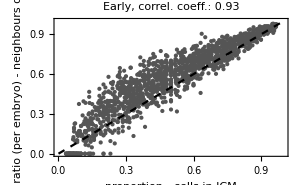
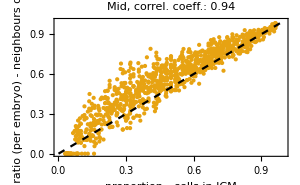
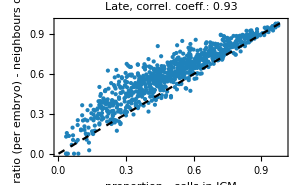
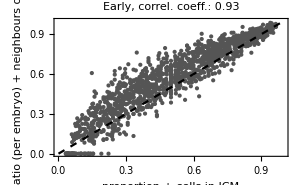
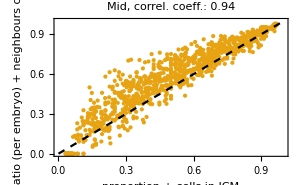
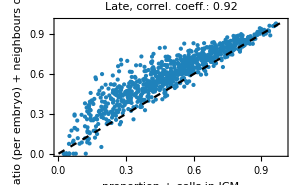
{            -Graphics--Graphics--Graphics-{negative, p=0.9},            -Graphics--Graphics--Graphics-{positive, p=0.9}}

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
(quadrantsComp=Import[FileNameJoin[{NotebookDirectory[],"Results\\quadrantsComp_LocalClust"<>ToString[#]<>".mx"}]];
stages=quadrantsComp[[All,1,3]];
cellNumberPerEmbryo=Length/@quadrantsComp[[All,2]];
plotRatiosNSortedRaw=calcPlotRatioSortedByCellNumber["","",quadrantsComp,stages,cellNumberPerEmbryo];
plotRatiosNSorted=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
plotRatiosNSortedByStage=Table[Select[plotRatiosNSorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
correlByStageM=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}];
correlByStageP=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}];
plotNeighbByStageM=Labeled[Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageM[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "],{"negative, p="<>ToString[#]},Top];
plotNeighbByStageP=Labeled[Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageP[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "],{"positive, p="<>ToString[#]},Top];
Print[{plotNeighbByStageM,plotNeighbByStageP}])&/@Range[0.1,0.9,0.1]
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageM_Cluster.png"}],plotNeighbByStageNm]*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"Figures","neighbByStageP_Cluster.png"}],plotNeighbByStageNp]*)
```

### p = 0 (same as alternating)

```mathematica
quadrantsComp=Import[FileNameJoin[{NotebookDirectory[],"Results\\quadrantsComp_LocalClust"<>ToString[0.]<>".mx"}]];
```

```mathematica
stages=quadrantsComp[[All,1,3]];
```

```mathematica
cellNumberPerEmbryo=Length/@quadrantsComp[[All,2]];
```

```mathematica
plotRatiosAllCells=calcPlotRatioAllCells["","",quadrantsComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSortedRaw=calcPlotRatioSortedByCellNumber["","",quadrantsComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSorted=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
plotRatiosNSortedRaw[[1]]
```

{Stage→3.,CellNumberEmbryo→14,CellNumberICM→5,NumPosCellsICM→2,NumNegCellsICM→3,MeanRatioNegNeighbNegCell→1/2,SEMRatioNegNeighbNegCell→0,MeanRatioPosNeighbPosCell→0,SEMRatioPosNeighbPosCell→0}

```mathematica
Length[plotRatiosNSortedRaw]-Length[plotRatiosNSorted]
```

0

```mathematica
plotRatiosNSortedByStage=Table[Select[plotRatiosNSorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

```mathematica
correlByStageM=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.353061,0.295356,0.293335}

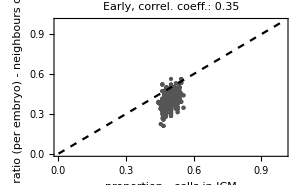
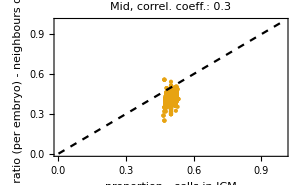
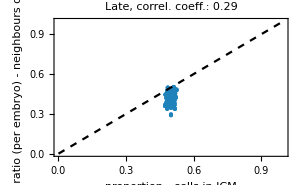

```mathematica
plotNeighbByStageM=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageM[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
correlByStageP=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}]
```

{0.348752,0.256253,0.243028}

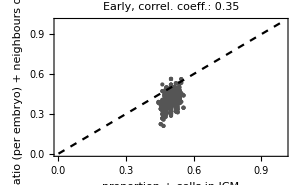
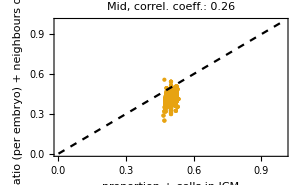
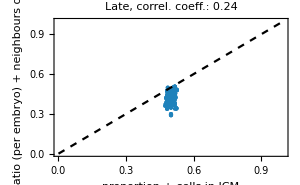

```mathematica
plotNeighbByStageP=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageP[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

### p = 1 (should always be (1,1))

```mathematica
quadrantsComp=Import[FileNameJoin[{NotebookDirectory[],"Results\\quadrantsComp_LocalClust"<>ToString[1.]<>".mx"}]];
```

```mathematica
stages=quadrantsComp[[All,1,3]];
```

```mathematica
cellNumberPerEmbryo=Length/@quadrantsComp[[All,2]];
```

```mathematica
plotRatiosAllCells=calcPlotRatioAllCells["","",quadrantsComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSortedRaw=calcPlotRatioSortedByCellNumber["","",quadrantsComp,stages,cellNumberPerEmbryo];
```

```mathematica
plotRatiosNSortedM=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&];
```

```mathematica
plotRatiosNSortedMByStage=Table[Select[plotRatiosNSortedM,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

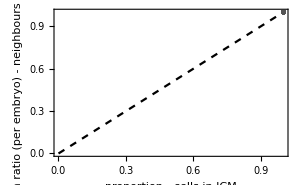
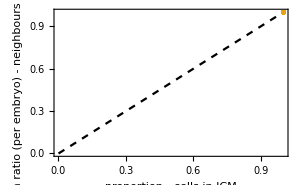
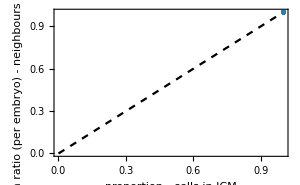

```mathematica
plotNeighbByStageM=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedMByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

```mathematica
plotRatiosNSortedP=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
```

```mathematica
plotRatiosNSortedPByStage=Table[Select[plotRatiosNSortedP,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
```

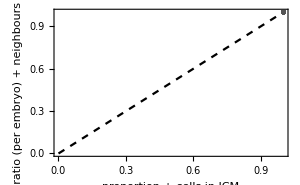
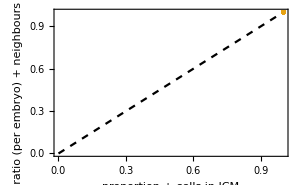
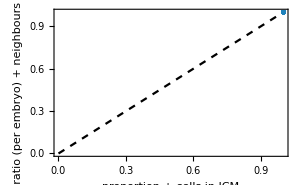

```mathematica
plotNeighbByStageP=Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedPByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"})],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "]
```

### p = 0.55

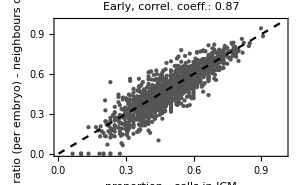
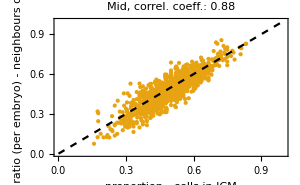
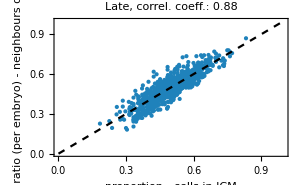
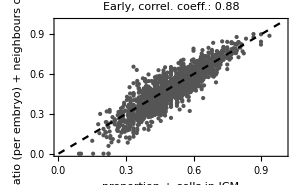
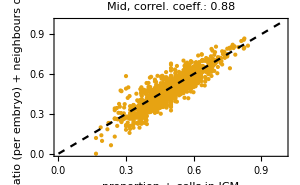
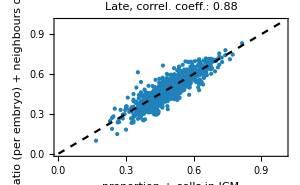
{            -Graphics--Graphics--Graphics-{negative, p=0.55},            -Graphics--Graphics--Graphics-{positive, p=0.55}}

```mathematica
(quadrantsComp=Import[FileNameJoin[{NotebookDirectory[],"Results\\quadrantsComp_LocalClust"<>ToString[#]<>".mx"}]];
stages=quadrantsComp[[All,1,3]];
cellNumberPerEmbryo=Length/@quadrantsComp[[All,2]];
plotRatiosNSortedRaw=calcPlotRatioSortedByCellNumber["","",quadrantsComp,stages,cellNumberPerEmbryo];
plotRatiosNSorted=Select[plotRatiosNSortedRaw,NumberQ["MeanRatioNegNeighbNegCell"/.#]&&NumberQ["MeanRatioPosNeighbPosCell"/.#]&];
plotRatiosNSortedByStage=Table[Select[plotRatiosNSorted,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];
correlByStageM=Table [N@Correlation[("NumNegCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioNegNeighbNegCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}];
correlByStageP=Table [N@Correlation[("NumPosCellsICM"/"CellNumberICM")/.plotRatiosNSortedByStage[[i]],"MeanRatioPosNeighbPosCell"/.plotRatiosNSortedByStage[[i]]],{i,1,3}];
plotNeighbByStageM=Labeled[Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumNegCellsICM"/"CellNumberICM"),"MeanRatioNegNeighbNegCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion - cells in ICM","mean ratio (per embryo)\n- neighbours of - cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageM[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "],{"negative, p="<>ToString[#]},Top];
plotNeighbByStageP=Labeled[Row[Table[Show[Graphics[{colour3[("Stage"/.#)/.{3.5->1,4.0->2,4.5->3}],Point[{("NumPosCellsICM"/"CellNumberICM"),"MeanRatioPosNeighbPosCell"}/.#]}&/@plotRatiosNSortedByStage[[i]],AspectRatio->1/GoldenRatio,Frame->{True,True,False,False},FrameStyle->Directive[Black,FontFamily->fontOption,14],ImageSize->300,FrameLabel->(Style[#,14,FontFamily->fontOption,Black]&/@{"proportion + cells in ICM","mean ratio (per embryo)\n+ neighbours of + cells"}),PlotLabel->Style[#,14,FontFamily->fontOption,Black]&@({"Early, ","Mid, ","Late, "}[[i]]<>"correl. coeff.: "<>ToString[Round[correlByStageP[[i]],0.01]])],Plot[x,{x,0,1},PlotStyle->Directive[Dashed,Black]]],{i,1,3}],"      "],{"positive, p="<>ToString[#]},Top];
Print[{plotNeighbByStageM,plotNeighbByStageP}])&@0.55
```

## Moran index

```mathematica
(*finalFNames=Select[FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"Results"}]],StringContainsQ[#,"localClustAll"]&];*)
```

```mathematica
(*finalFNames*)
```

```mathematica
(*data=Flatten[Import[#]&/@finalFNames,1];*)
```

```mathematica
(*nucleiFeatures=("NucleiFeatures"/.data);*)
```

```mathematica
(*staging=("Staging"/.data);*)
```

```mathematica
(*dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];*)
```

```mathematica
(*moranValuesAll=(("p="<>ToString[#])->(MapThread[Rule,{{"Stage","Embryo","Experiment","+-Moran"},#}]&/@(Table[Join[staging[[i,{3,2,1}]],{({values,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"+","localClusterFate"<>ToString[#]];If [Length[DeleteDuplicates[values]]>1,calcMoranI[values,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}])))&/@Range[0,0.9,0.1];*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"Results","moranValuesLocalClustAll.mx"}],moranValuesAll]*)
```

```mathematica
moranValuesAll=Import[FileNameJoin[{NotebookDirectory[],"Results","moranValuesLocalClustAll.mx"}]];
```

number of embryos discarded

```mathematica
Table[Length[Cases["+-Moran"/.moranValuesAll[[i,2]],"only one cell type"]],{i,1,Length[moranValuesAll]}]
```

{0,0,0,1,0,4,3,15,57,416}

```mathematica
Table[Length[Cases["+-Moran"/.moranValuesAll[[i,2]],Except["only one cell type"]]],{i,1,Length[moranValuesAll]}]
```

{3690,3690,3690,3689,3690,3686,3687,3675,3633,3274}

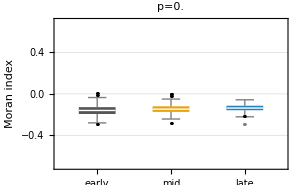

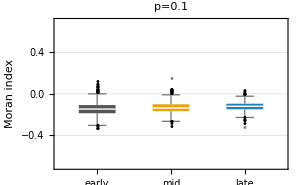

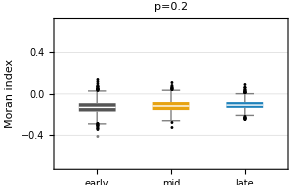

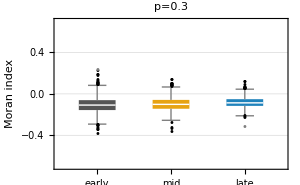

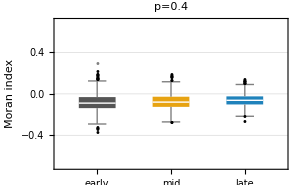

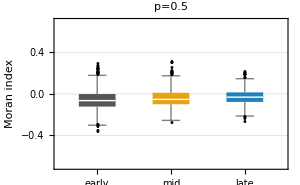

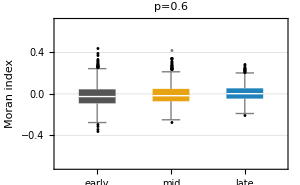

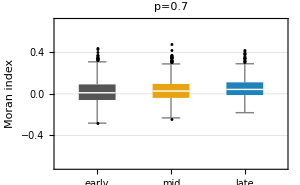

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
(moranValues=("p="<>ToString[#])/.moranValuesAll;
moranValuesByStage=Table[Select[moranValues,("Stage"/.#)==i&],{i,{3.5,4.0,4.5}}];plotMoran=BoxWhiskerChart[Cases[#,Except["only one cell type"]]&/@("+-Moran"/.moranValuesByStage),"Outliers",ChartLabels->{"early","mid","late"},ImageSize->300,PlotLabel->Style[("p="<>ToString[#]),Black,20],PlotRange->{-0.7,0.7},FrameLabel-> {None,"Moran index"},FrameStyle->Directive[Black,20],ChartStyle->(colour3[#]&/@{1,2,3}),GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]];Print[plotMoran])&/@Range[0,0.9,0.1]
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"Figures","moran_Cluster.png"}],plotMoran]*)
```

```mathematica
plotData=Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[moranValuesAll[[i,2]],("Stage"/.#)>3.0&]),{i,1,Length[moranValuesAll]}];
```

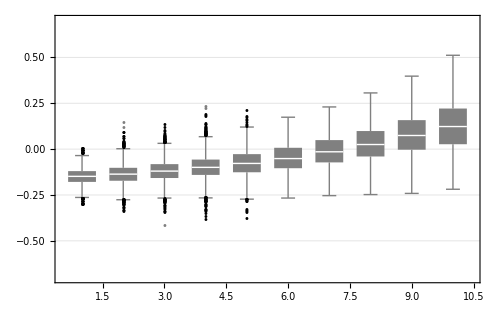

```mathematica
plotMoranAll=BoxWhiskerChart[plotData,"Outliers",ChartLabels->{(ToString/@Range[0,0.9,0.1])},ImageSize->500,PlotRange->{-0.7,0.7},FrameLabel-> {"Clustering probability","Moran index"},FrameStyle->Directive[Black,20],ChartStyle->Gray,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

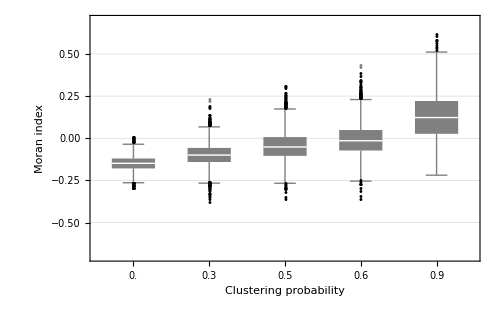

```mathematica
plotMoranSelected=BoxWhiskerChart[plotData[[{1,4,6,7,10}]],"Outliers",ChartLabels->{(ToString/@Range[0,0.9,0.1])[[{1,4,6,7,10}]]},ImageSize->500,(*PlotLabel->("p="<>ToString[#]),*)PlotRange->{-0.7,0.7},FrameLabel-> {"Clustering probability","Moran index"},FrameStyle->Directive[Black,20],ChartStyle->Gray,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Figures","moranValuesClustScan.png"}],plotMoranSelected]
```

### include p = 0.55

```mathematica
(*finalFNames=Select[FileNames["*FinalData.mx",FileNameJoin[{NotebookDirectory[],"Results"}]],StringContainsQ[#,"localClust0.55"]&];*)
```

```mathematica
(*finalFNames*)
```

```mathematica
(*data=Flatten[Import[#]&/@finalFNames,1];*)
```

```mathematica
(*nucleiFeatures=("NucleiFeatures"/.data);*)
```

```mathematica
(*staging=("Staging"/.data);*)
```

```mathematica
(*dcgGraphs=Transpose[{staging,("DelaunayCellGraph"/.("GlobalFeatures"/.#))&/@data}];*)
```

```mathematica
(*moranValues=(("p="<>ToString[#])->(MapThread[Rule,{{"Stage","Embryo","Experiment","+-Moran"},#}]&/@(Table[Join[staging[[i,{3,2,1}]],{({values,weights}=prepareDataMoran[nucleiFeatures[[i]],dcgGraphs[[i,2]],"+","localClusterFate"<>ToString[#]];If [Length[DeleteDuplicates[values]]>1,calcMoranI[values,weights],"only one cell type"])}],{i,1,Length[nucleiFeatures]}])))&@0.55;*)
```

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"Results","moranValuesLocalClust0.55.mx"}],moranValues]*)
```

```mathematica
moranValues=Import[FileNameJoin[{NotebookDirectory[],"Results","moranValuesLocalClust0.55.mx"}]];
```

```mathematica
plotData=Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[moranValues[[2]],("Stage"/.#)>3.0&]);
```

```mathematica
moranValuesAll=Import[FileNameJoin[{NotebookDirectory[],"Results","moranValuesLocalClustAll.mx"}]];
```

```mathematica
plotDataAll=Join[Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[moranValuesAll[[i,2]],("Stage"/.#)>3.0&]),{i,1,6}],{plotData},Table[Cases[#,Except["only one cell type"]]&@("+-Moran"/.Select[moranValuesAll[[i,2]],("Stage"/.#)>3.0&]),{i,7,Length[moranValuesAll]}]];
```

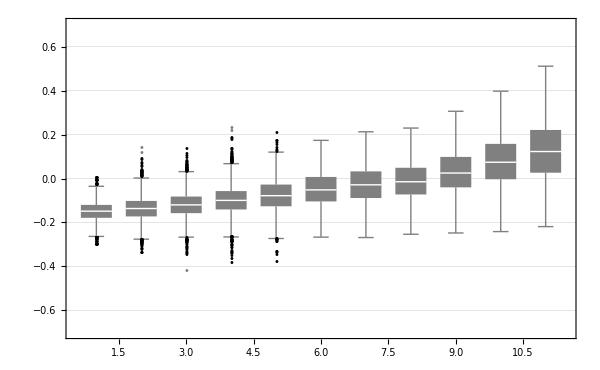

```mathematica
plotMoranAll=BoxWhiskerChart[plotDataAll,"Outliers",ChartLabels->{ToString/@Join[Range[0,0.5,0.1],{0.55},Range[0.6,0.9,0.1]]},ImageSize->600,PlotRange->{-0.7,0.7},FrameLabel-> {"Clustering probability","Moran index"},FrameStyle->Directive[Black,20],ChartStyle->Gray,GridLines->{None,Automatic},GridLinesStyle->Directive[Gray,Thickness[0.001]]]
```

```mathematica
exportDataForHypothesisTest=Join@@@Transpose[{Partition[Join[Range[0,0.5,0.1],{0.55},Range[0.6,0.9,0.1]],1],plotDataAll}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Results","localClustDataForWelchTest.json"}],exportDataForHypothesisTest]
```